# 2. domača naloga

## 1. naloga

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte lastne vrednosti in lastne vektorje matrike .
c)  Narišite lastne vektorje matrike .
d) Izračunajte karakteristični polinom matrike .
e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .
f) Rešite matrično enačbo .

```mathematica
A[n_, m_]:=Table[i+j, {i,1,n}, {j,1,m}]
A[3,3]
mat=A[3,3]
Eigenvalues[mat]
Eigenvectors[mat]
```

{{2,3,4},{3,4,5},{4,5,6}}

{{2,3,4},{3,4,5},{4,5,6}}

{6+√42,6-√42,0}

{{-(-17-2 √42)/(23+4 √42),-(-20-3 √42)/(23+4 √42),1},{-(17-2 √42)/(-23+4 √42),-(20-3 √42)/(-23+4 √42),1},{1,-2,1}}

```mathematica
Graphics3D[Arrow[{{0,0,0}, #}]&/@%]
```

-Graphics3D-

```mathematica
{vals, vecs}=Eigensystem[mat];
P=Transpose[vecs];
Pinv=Inverse[P];
G=DiagonalMatrix[vals];
Simplify[P.G.Pinv]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
X=Inverse[mat+P-G]
```

{{(-32+7 √42-140/(-23+4 √42)+(21 √42)/(-23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(9+119/(-23+4 √42)-(14 √42)/(-23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(19-5 √42+49/(-23+4 √42)-(9 √42)/(-23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42)))},{(-6-140/(23+4 √42)-(21 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(-53-7 √42+119/(23+4 √42)+(14 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(27+3 √42+49/(23+4 √42)+(9 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42)))},{(28-5 √42+100/(-23+4 √42)-(15 √42)/(-23+4 √42)+120/(23+4 √42)+(18 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(39+6 √42-85/(-23+4 √42)+(10 √42)/(-23+4 √42)-102/(23+4 √42)-(12 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(-43-2 √42+5/(-23+4 √42)+(2 √42)/(-23+4 √42)-10/(23+4 √42)+(4 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42)))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42)))}}

## 2. naloga

Imamo klančino z naklonom 30 stopinj dolžine 10m. Na dnu klančine se nahaja ravnina dolžine 10m. Na levem in desnem robu se nahaja stena (glej sliko). 
Kroglico z radijem 10cm spustimo na vrhu klanca, da se začne gibati pod vplivom gravitacije. Predpostavite lahko, da med kroglico in podlago ni trenja in 
da se zaradi kotaljenja energija ne izgublja. Ko pride kroglica na dno klanca, se giblje v vodoravni smeri z enako velikim vektorjem hitrosti (predpostavi, 
da je kot dovolj majhen, da na pride do odboja). 
Simulirajte kotaljenje kroglice po klančini in ravnini, ki se odbija od desnega roba.
Za gravitacijski pospešek vzemite g = 9.81, začetna hitrost kroglice naj bo v0 = 0.

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, začetno hitrost in radij kroglice.

b) Nariši klančino, tla in obe steni.

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče.

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

e) Definiraj funkcijo `desniRob`, ki sprejme središče kroglice in vrne `True`, če je kroglica trčila ob desni rob.

f) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α.

g) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

h) Definiraj funkcijo `hitrostSKlanca`, ki sprejme vektor trenutne hitrosti kroglice in vrne novo hitrost, ki jo dobi kroglica, ko s klanca preide na ravni del.

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice.

```mathematica
g=9.81
alpha = 30 Degree
dolzklanec = 10
dolzravnina=10
r=0.1
v0=0
```

9.81

30 °

10

10

0.1

0

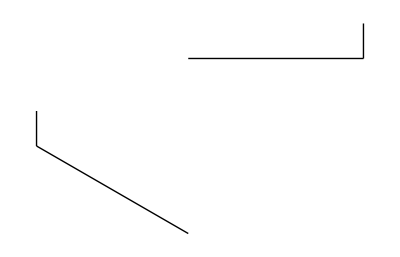

```mathematica
Graphics[{
Line[{{0,0},{dolzklanec*Cos[alpha],-dolzklanec*Sin[alpha]}}],
Line[{{dolzklanec*Cos[alpha],-dolzklanec*Sin[alpha]},{dolzklanec*Cos[alpha]+dolzravnina,dolzklanec*Sin[alpha]}}],
Line[{{0,0},{0,2}}],
Line[{{dolzklanec*Cos[alpha]+dolzravnina,dolzklanec*Sin[alpha]},{dolzklanec*Cos[alpha]+dolzravnina,dolzklanec*Sin[alpha]+2}}]
}]
```